{{θ→InterpolatingFunction[{{0., 60.}}, <>]}}

Magnetic Pendulum Motion:

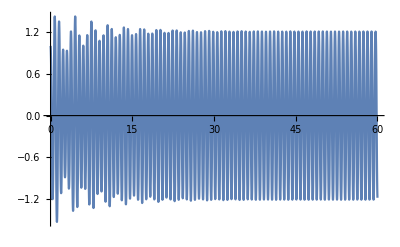

```mathematica
m=1/4;
l=1/4;
g=10;
A=1/32;
b=1/1000;
k=4;
ω=k*Sqrt[g/l];
σ=2;
time=60;
Needs["VariationalMethods`"]
eqs=m*(l/2)^2*θ''[t]+b*θ'[t]+m*g*(l/2)*Sin[θ[t]]==A*Sin[ω*t]*Exp[σ*Cos[θ[t]]];
s=NDSolve[{eqs,θ[0]==1,θ'[0]==0},θ,{t,0,time}] 

"Magnetic Pendulum Motion:"
Plot[Evaluate[θ[t]/.s],{t,0,time}]
plt=Plot[-50,{x,-l,l},PlotRange->{-l,l},AxesStyle->{Directive[0.1,Black],Directive[0.1,Black]}, Ticks->None];
Animate[Show[plt,Graphics[{Blue,CapForm["Round"],Thickness[(m/l)/100],Line[{{0,0},{l*Sin[θ[t]],-l*Cos[θ[t]]}}]}],AspectRatio->Automatic]/.s,{t,0,time},AnimationRate->1, AnimationRunning->False,RefreshRate->120]
```